```mathematica
<<ComputerArithmetic`
```

## Atomic to Physical Unit Conversions

```mathematica
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."]

(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."]

(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."]
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

## Solver

```mathematica
solver=Function[
{orbit,static,microwave,tmax},
ClearAll[x,z,t,sol];(* Solver variables *)
ClearAll[v0,r0,vx0,vz0,x0,z0];

(* Unpack *)
{en0,l0,θrot,dv}=orbit;
{fpulse}=static;
{fmw,ω,α,toff,τring}=microwave;

(* Orbital variables *)
(* Derived orbital conditions *)
{r0,v0}=orbitic[en0,l0];

(* Rotate angular momentum about r *)
x0=r0*Sin[θrot];
z0=-r0*Cos[θrot];
(* Print["Initial Position ",{x0,z0}] *)
vx0=dv*v0*Cos[θrot];
vz0=dv*v0*Sin[θrot];
(* Print["Initial Velocity ",{vx0,vz0}] *)

(* Solver *)
sol=NDSolve[
{x''[t]==-x[t]/(x[t]^2+z[t]^2)^(3/2),
x'[0]==vx0,
x[0]==x0,
z''[t]==-z[t]/(x[t]^2+z[t]^2)^(3/2)
-fpulse*If[t<toff,1,0]
-fmw*Sin[ω*t+α]*
If[t<toff,1,E^(-(t-toff)/τring)],
z'[0]==vz0,
z[0]==z0},
{x,z},
{t,0,tmax},
AccuracyGoal->13,(* Accuracy and Precision to get energy conservation *)
PrecisionGoal->13,
MaxSteps->1000000]
];
```

```mathematica
Solve[{0==1/2x^2-1/y,b==x*y},{x,y}]
```

{{x→2/b,y→b^2/2}}

## Single Runs

### Functions

```mathematica
orbitic=Function[{en0,l0},
If[en0==0,r=l0^2/2,r=(-1+√(1+2*en0*l0^2))/(2*en0)];
If[en0==0,v=2/l0,v=(1+√(1+2*en0*l0^2))/l0];
{r,v}
];
enfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];
rfunc=Function[{x,z},
√(x^2+z^2)];
```

### Test Case

#### settings

{-61.4143,249.891}

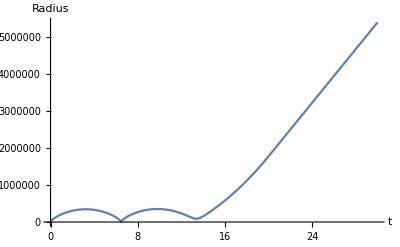

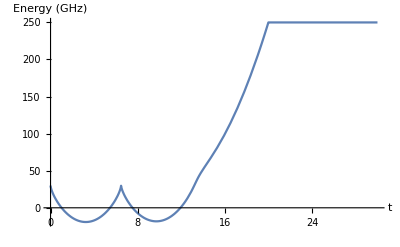

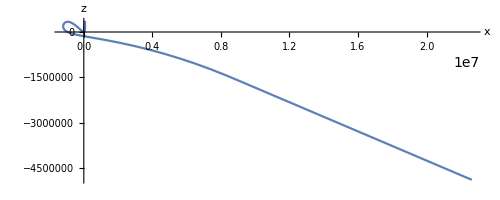

```mathematica
(* orbit -> {en0,l0,θrot,dv} *)
en0=30*enAU1GHz; (* according to plots *)
l0=√(3*(3+1));(* s=0,p=1,d=2,f=3 *)
θrot=0;(* is this up or down? *)
dv=1;(* is this +/- x? *)
orbit={en0,l0,θrot,dv};
(* static -> {fstx,fstz,fpulse} *)
fpulse=112*fAU1mVcm; (* according to plots *)
static={fpulse};
(* microwave -> {fmw,ω,α,toff,τring} *)
fmw=0*1000*fAU1mVcm; (* according to plot *)
ω=2*π*15.9/tAU1ns; (* 15.9 GHz exp setup *)
α=2/102*π; (* according to plot *)
toff=20*tAU1ns;(* exp setup *)
τring=10*tAU1ns;(* ringdown est. *)
microwave={fmw,ω,α,toff,τring};
(* tmax *)
tmax=30*tAU1ns; ; (* set to preference *)
sol=solver[orbit,static,microwave,tmax];
ttest=20.01*tAU1ns;
efinal=1/enAU1GHz*(enfunc[x[ttest],z[ttest],x'[ttest],z'[ttest]]/.sol)[[1]];
Print[{-2*√fpulse/enAU1GHz,efinal}];
Plot[rfunc[x[t*tAU1ns],z[t*tAU1ns]]/.sol,{t,0,1.5*ttest/tAU1ns},AxesLabel->{"t","Radius"}]
Plot[1/enAU1GHz*enfunc[x[t*tAU1ns],z[t*tAU1ns],x'[t*tAU1ns],z'[t*tAU1ns]]/.sol,{t,0,1.5*ttest/tAU1ns},AxesLabel->{"t","Energy (GHz)"}]
ParametricPlot[{x[t]*10,z[t]}/.sol,{t,0,1.5*ttest},AxesLabel->{"x","z"}]
```

{0.721772}

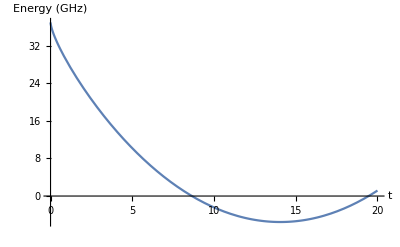

```mathematica
(1/enAU1GHz*enfunc[x[t*tAU1ns],z[t*tAU1ns],x'[t*tAU1ns],z'[t*tAU1ns]]/.sol)/.t->(ttest*0.99/tAU1ns)
Plot[1/enAU1GHz*enfunc[x[t*tAU1ns],z[t*tAU1ns],x'[t*tAU1ns],z'[t*tAU1ns]]/.sol,{t,0,ttest/tAU1ns},AxesLabel->{"t","Energy (GHz)"}]
```

#### solve

```mathematica
sol=solver[orbit,static,microwave,tmax];
```

#### plots

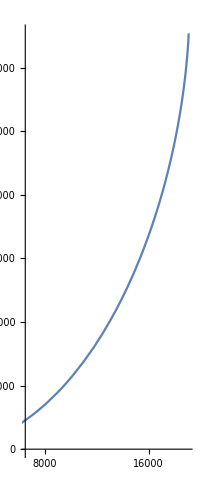

```mathematica
ParametricPlot[{x[t]*10,z[t]}/.sol,{t,0,tmax}]
```

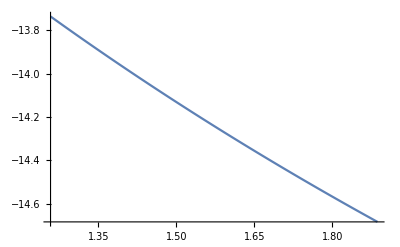

```mathematica
Plot[1/enAU1GHz*enfunc[x[t*tAU1ns],z[t*tAU1ns],x'[t*tAU1ns],z'[t*tAU1ns]]/.sol,{t,(tmax-2*π/ω*10)/tAU1ns,tmax/tAU1ns},PlotRange->All]
```

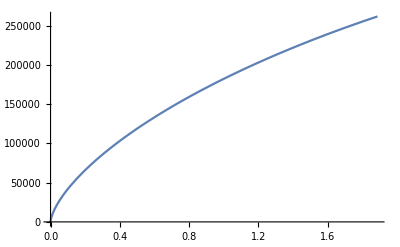

```mathematica
Plot[rfunc[x[t*tAU1ns],z[t*tAU1ns]]/.sol,{t,0,tmax/tAU1ns}]
```

## Final Energy vs. Phase Runs

```mathematica
ClearAll[results,en0,l0,θrot,dv,orbit,fpulse,static,fmw,ω,toff,τring,microwave,tmax,sol,efinal,α]
results={};
(* SetSharedVariable[results] *)
ParallelDo[
(* orbit -> {en0,l0,θrot,dv} *)
en0=200*enAU1GHz; (* according to plots *)
l0=√(3*(3+1));(* s=0,p=1,d=2,f=3 *)
θrot=0;(* is this up or down? *)
dv=1;(* is this +/- x? *)
orbit={en0,l0,θrot,dv};
(* static -> {fstx,fstz,fpulse} *)
fpulse=0*fAU1mVcm; (* according to plots *)
static={fpulse};
(* microwave -> {fmw,ω,α,toff,τring} *)
fmw=4*1000*fAU1mVcm; (* according to plot *)
ω=2*π*15.9/tAU1ns; (* 15.9 GHz exp setup *)
(*α=7/6*π;*) (* according to plot *)
toff=20*tAU1ns;(* exp setup *)
τring=10*tAU1ns;(* ringdown est. *)
microwave={fmw,ω,α,toff,τring};
(* tmax *)
tmax=30*2*π/ω; (* set to preference *)
sol=Check[solver[orbit,static,microwave,tmax],Indeterminate];
efinal=If[Length[sol]!=0,
Check[1/(10*2*π/ω*enAU1GHz)*NIntegrate[enfunc[x[t]/.sol,z[t]/.sol,x'[t]/.sol,z'[t]/.sol][[1]],{t,10*2*π/ω,20*2*π/ω}],Indeterminate],
Indeterminate
]; 
erec=efinal-en0/enAU1GHz;
If[erec===Indeterminate,erec=NaN];
AppendTo[results,{N[α],erec}];
Print[{N[α],erec}],
{α,0,2π-π/102,π/102}]
results=SortBy[results,First];
Export["C:\\Users\\edmag\\Documents\\Work\\Electron Motion\\testing\\results.txt",results,"tsv"]
```

C:\Users\edmag\Documents\Work\Electron Motion\testing\results.txt

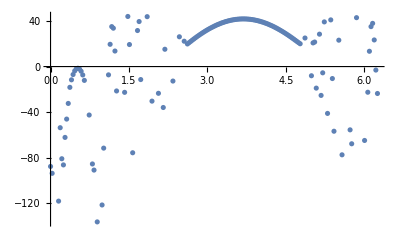

```mathematica
ListPlot[results]
```

```mathematica
fmw={2,4,6}*1000*fAU1mVcm; 
ω=2*π*15.9/tAU1ns;
3/2*fmw/(ω^(2/3))/enAU1GHz
```

{21.3165,42.6329,63.9494}

```mathematica
ω
```

2.41653×10^-6

```mathematica
fmw
```

{3.88938×10^-10,7.77876×10^-10,1.16681×10^-9}

```mathematica
fAU1mVcm
```

1.94469×10^-13

```mathematica
enAU1GHz
```

1.51983×10^-7

## Failed Runs

### Parallel Loop through all Bad Conditions

```mathematica
Length[data]
```

2821

```mathematica
<<ComputerArithmetic`
(* Import Error Contiions*)
data=Import[FileNameJoin[{NotebookDirectory[],"ErrorConditions.txt"}],"Data"];
(* Add space for new values *)
placeholder=Table["none",{i,1,Length[data]}];
data=Transpose[Append[Transpose[data],placeholder]];
placeholder=Table[NaN,{i,1,Length[data]}];
data=Transpose[Append[Transpose[data],placeholder]];
data=Transpose[Append[Transpose[data],placeholder]];
data=Transpose[Append[Transpose[data],placeholder]];
(* Properly give it a header *)
data[[1]]={"","E0","Ep","dL","phi","th_LRL","Error","Dlow","Dhigh","enfinal"};
progress=0;
length=Length[data];
SetSharedVariable[data,progress,length];
Monitor[
ParallelDo[
(* Read Settings *)
(* orbit -> {en0,l0,θrot,dv} *)
(* en0=-20*enAU1GHz; (* according to plots *) *)
en0=Round[data[[i,2]],1]*enAU1GHz;
l0=√(3*(3+1));(* s=0,p=1,d=2,f=3 *)
(* θrot=0;(* is this up or down? *) *)
θrot=Round[data[[i,6]],1]*π;
(* dv=-1; (* is this +/- x? *) *)
dv=Round[data[[i,4]],1];
orbit={en0,l0,θrot,dv};
(* static -> {fstx,fstz,fpulse} *)
(* fpulse=400*0.72*fAU1mVcm; (* according to plots *) *)
fpulse=Round[data[[i,3]]/0.72,1]*0.72*fAU1mVcm;
static={fpulse};
(* microwave -> {fmw,ω,α,toff,τring} *)
fmw=4*1000*fAU1mVcm; (* according to plot *)
ω=2*π*15.9/tAU1ns; (* 15.9 GHz exp setup *)
(* α=132/100*π; (* according to plot *) *)
α=Round[data[[i,5]],1]*π/100;
(* dα=π/100; *)
toff=20*tAU1ns;(* exp setup *)
τring=10*tAU1ns;(* ringdown est. *)
microwave={fmw,ω,α,toff,τring};
(* tmax *)
tmax=toff+5*τring; (* set to preference *)

(* Solve *)
(* Temp stream to redirect messages to *)
 stream=OpenWrite[];
$Messages={stream}; 
(* Solve and reset message stream *)
soldata=EvaluationData[solver[orbit,static,microwave,tmax]];
Close[stream];
$Messages={Streams[][[1]]};
(* Extract useful info *)
sol=soldata["Result"];
(* Sometimes there's no error. Why? *)
If[soldata["Success"]==False,
errmess=ToString[Extract[soldata["MessagesExpressions"],{1,1,1,2}]];
,
errmess="NOERR";];
domain=(x/.sol[[1,1]])["Domain"];
tf=Max[domain];
enfinal=enfunc[x[tf]/.sol,z[tf]/.sol,x'[tf]/.sol,z'[tf]/.sol][[1]];

(* report, all in a.u. *)
data[[i,2]]=N[en0];
data[[i,3]]=N[fpulse];
data[[i,4]]=N[dv];
data[[i,5]]=N[α];
data[[i,6]]=N[θrot];
data[[i,7]]=errmess;
data[[i,8]]=Min[domain];
data[[i,9]]=Max[domain];
data[[i,10]]=enfinal;
progress=progress+1;
,{i,2,Length[data]}]
,{progress,length,ProgressIndicator[progress/length]}]
Export[FileNameJoin[{NotebookDirectory[],"ErrorMessages.txt"}],data,"csv"]
```

C:\Users\labuser\Documents\2D-Comp-Model\computation\ErrorMessages.txt

```mathematica
tmax/tAU1ns
```

70.

### Functions

```mathematica
orbitic=Function[{en0,l0},
If[en0==0,r=l0^2/2,r=(-1+√(1+2*en0*l0^2))/(2*en0)];
If[en0==0,v=2/l0,v=(1+√(1+2*en0*l0^2))/l0];
{r,v}
];
enfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];
rfunc=Function[{x,z},
√(x^2+z^2)];
lfunc=Function[{x,z,vx,vz},
z*vx-x*vz];
```

### Single Run

#### settings

```mathematica
(* orbit -> {en0,l0,θrot,dv} *)
en0=-20*enAU1GHz; (* according to plots *)
l0=√(3*(3+1));(* s=0,p=1,d=2,f=3 *)
θrot=0;(* is this up or down? *)
dv=1; (* is this +/- x? *)
orbit={en0,l0,θrot,dv};
(* static -> {fstx,fstz,fpulse} *)
fpulse=360*0.72*fAU1mVcm; (* according to plots *)
static={fpulse};
(* microwave -> {fmw,ω,α,toff,τring} *)
fmw=4*1000*fAU1mVcm; (* according to plot *)
ω=2*π*15.9/tAU1ns; (* 15.9 GHz exp setup *)
α=62/100*π; (* according to plot *)
(* dα=π/100; *)
toff=20*tAU1ns;(* exp setup *)
τring=10*tAU1ns;(* ringdown est. *)
microwave={fmw,ω,α,toff,τring};
(* tmax *)
tmax=toff+5*τring; (* set to preference *)
```

#### solve

```mathematica
(* Solve *)
(* Temp stream to redirect messages to *)
 stream=OpenWrite[];
$Messages={stream}; 
(* Solve and reset message stream *)
soldata=EvaluationData[solver[orbit,static,microwave,tmax]];
Close[stream];
$Messages={Streams[][[1]]};
(* Extract useful info *)
sol=soldata["Result"];
If[soldata["Success"]==False,
errmess=ToString[Extract[soldata["MessagesExpressions"],{1,1,1,2}]];
,
errmess="NOERR";]
domain=(x/.sol[[1,1]])["Domain"];
tf=Max[domain];
enfinal=enfunc[x[tf]/.sol,z[tf]/.sol,x'[tf]/.sol,z'[tf]/.sol][[1]];
(* report *)
Print["Error:\t",errmess]
Print["Domain:\t",domain]
Print["Energy (GHz): \t",enfinal/enAU1GHz]
```

Error:	ndsz

Domain:	{{0.,5.66503×10^8}}

Energy (GHz): 	-38.6378

```mathematica
soldata
```

<|Result:>{{x→                                      8
InterpolatingFunction[{{0., 5.66503 10 }}, <>],z→                                      8
InterpolatingFunction[{{0., 5.66503 10 }}, <>]}},Success→False,FailureType→MessageFailure,OutputLog→{},Messages→{At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.},MessagesText→{                                  8
NDSolve::ndsz : At t == 5.66503 10 , step size is effectively zero; singularity or stiff system suspected.},MessagesExpressions→{Hold[Message[NDSolve::ndsz,t,5.66503×10^8]]},Timing→5.71,AbsoluteTiming→5.699,InputString→solver[orbit, static, microwave, tmax]|>

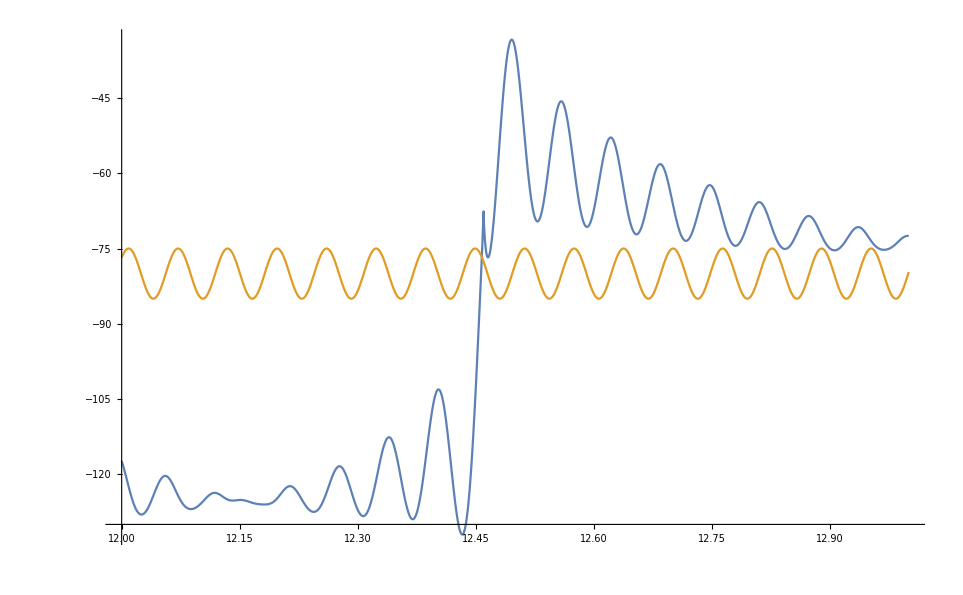

```mathematica
Plot[{enfunc[x[t*tAU1ns]/.sol,z[t*tAU1ns]/.sol,x'[t*tAU1ns]/.sol,z'[t*tAU1ns]/.sol][[1]]/enAU1GHz,5*Sin[ω*t*tAU1ns+α]-80} ,(* {t,domain[[1,1]]/tAU1ns,domain[[1,2]]/tAU1ns}] *)
{t,12,13}]
```

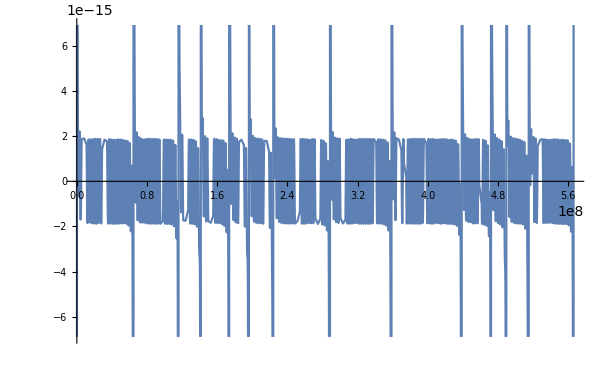

```mathematica
Plot[D[z[τ]/.sol,{τ,3}]/.τ->t,{t,domain[[1,1]],domain[[1,2]]}]
```

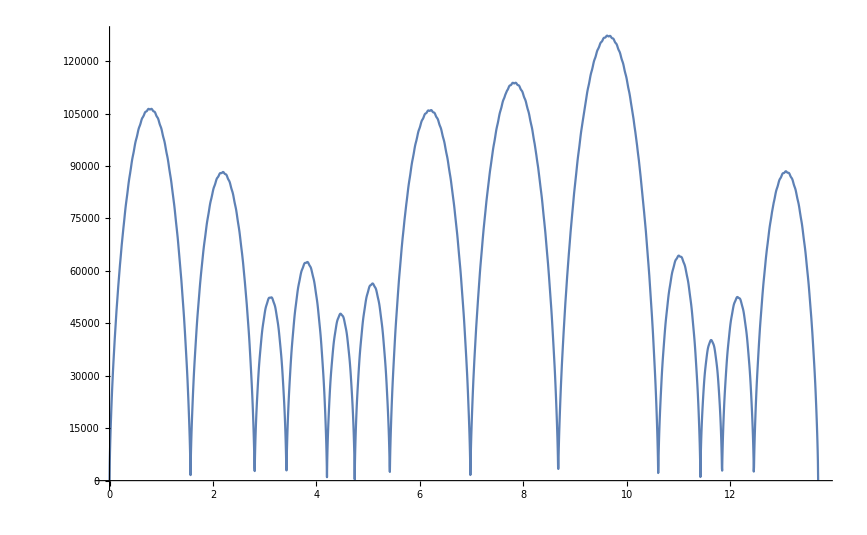

```mathematica
Plot[rfunc[x[t*tAU1ns]/.sol,z[t*tAU1ns]/.sol],{t,domain[[1,1]]/tAU1ns,domain[[1,2]]/tAU1ns}]
```

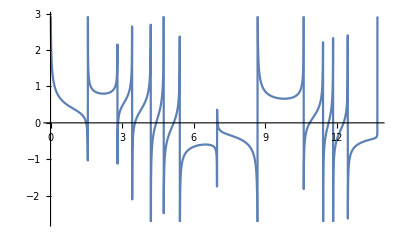

```mathematica
Plot[ArcTan[z[t*tAU1ns]/.sol,x[t*tAU1ns]/.sol]*180/π,{t,domain[[1,1]]/tAU1ns,domain[[1,2]]/tAU1ns}]
```

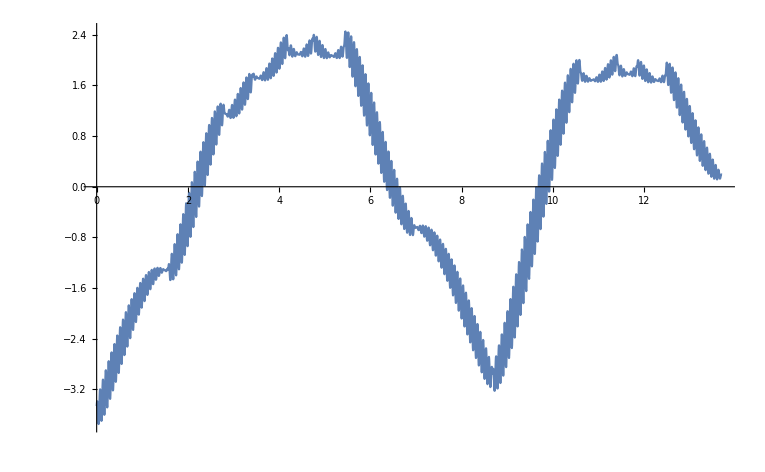

```mathematica
Plot[lfunc[x[t*tAU1ns]/.sol,z[t*tAU1ns]/.sol,x'[t*tAU1ns]/.sol,z'[t*tAU1ns]/.sol],{t,domain[[1,1]]/tAU1ns,domain[[1,2]]/tAU1ns}]
```

```mathematica
20/(domain[[1,2]]/tAU1ns)
```

1.45953

```mathematica
Manipulate[
ParametricPlot[{x[t*tAU1ns]*100,z[t*tAU1ns]}/.sol,{t,domain[[1,1]]/tAU1ns,n}],
{n,0.1,domain[[1,2]]/tAU1ns}]
```

## Experimental Runs

### Functions

```mathematica
orbitic=Function[{en0,l0},
If[en0==0,r=l0^2/2,r=(-1+√(1+2*en0*l0^2))/(2*en0)];
If[en0==0,v=2/l0,v=(1+√(1+2*en0*l0^2))/l0];
{r,v}
];
enfunc=Function[{x,z,vx,vz},
1/2*(vx^2+vz^2)-1/√(x^2+z^2)];
rfunc=Function[{x,z},
√(x^2+z^2)];
```

### Parallel Execution

```mathematica
Monitor[Do[
ClearAll[results,en0,l0,θrot,dv,orbit,static,fmw,ω,toff,τring,microwave,tmax,sol,efinal,α];
SetDirectory[NotebookDirectory[]];
(* ---------- *)
(* Execution *)
results={};
SetSharedVariable[results];
(* orbit -> {en0,l0,θrot,dv} *)
en0=-20*enAU1GHz; (* according to plots *)
l0=√(3*(3+1));(* s=0,p=1,d=2,f=3 *)
(* θrot=0; *)(* is this up or down? *)
(* dv=1; *)(* is this +/- x? *)
orbit={en0,l0,θrot,dv};
(* static -> {fstx,fstz,fpulse} *)
(* fpulse=10*0.72*fAU1mVcm; *) (* according to plots *)
static={fpulse};
(* microwave -> {fmw,ω,α,toff,τring} *)
fmw=4*1000*fAU1mVcm; (* according to plot *)
ω=2*π*15.9/tAU1ns; (* 15.9 GHz exp setup *)
(*α=7/6*π;*) (* according to plot *)
dα=π/100;
toff=20*tAU1ns;(* exp setup *)
τring=10*tAU1ns;(* ringdown est. *)
microwave={fmw,ω,α,toff,τring};
(* tmax *)
tmax=toff+5*τring; (* set to preference *)
(* tmax=1*tAU1ns; *)
(* Parallel Execution *)
tstart=AbsoluteTime[];
Monitor[
ParallelDo[
sol=Quiet[Check[solver[orbit,static,microwave,tmax],Indeterminate]];
efinal=If[sol===Indeterminate,
Indeterminate,
Check[
1/(10*2*π/ω*enAU1GHz)*NIntegrate[enfunc[x[t]/.sol,z[t]/.sol,x'[t]/.sol,z'[t]/.sol][[1]],{t,tmax-10*2*π/ω,tmax}],
Indeterminate]
]; 
erec=efinal*enAU1GHz;
If[erec===Indeterminate,erec=NaN];
AppendTo[results,{N[dv],N[θrot],N[α],erec}];
(* Print[{N[α],erec}]; *),
{α,0,2π-dα,dα},{dv,{-1,1}},{θrot,{0,π}}]
,ProgressIndicator[Length[results],{0,2*π/dα*4}]];
tend=AbsoluteTime[];
(* ---------- *)
(* Export Results *)
results=SortBy[results,{#[[1]],#[[2]],#[[3]]}&];
tidy=Function[{x},ToString[FortranForm[N[x]]]];
fname="results\\"<>StringReplace[DateString[Now,"ISODateTime"],":"->"-"]<>".txt";
header=StringJoin[
"# Filename\t"<>Directory[]<>fname<>"\n",
"# Source\t"<>NotebookFileName[]<>"\n",
"# Note\t"<>"A phase vs. final energy run at given parameters for the StaPD computational model."<>"\n",
"# Date\t"<>DateString[Now,"ISODateTime"]<>"\n",
"# E0\t"<>tidy[en0]<>"\n",
"# l0\t"<>tidy[l0]<>"\n",
(* "# th_LRL\t"<>tidy[θrot]<>"\n", *)
(* "# dL\t"<>tidy[dv]<>"\n", *)
"# Ep\t"<>tidy[fpulse]<>"\n",
"# Emw\t"<>tidy[fmw]<>"\n",
"# fmw\t"<>tidy[ω]<>"\n",
"# toff\t"<>tidy[toff]<>"\n",
"# tring\t"<>tidy[τring]<>"\n",
"# tmax\t"<>tidy[tmax]<>"\n",
"dL"<>"\t"<>"th_LRL"<>"\t"<>"phi"<>"\t"<>"enfinal"<>"\n"
];
Put[fname];
stream=OpenWrite[fname];
WriteString[stream,header]
Do[
wstring=StringJoin[tidy[results[[i,1]]],"\t",tidy[results[[i,2]]],"\t",tidy[results[[i,3]]],"\t",tidy[results[[i,4]]],"\n"];
WriteString[stream,wstring]
,{i,1,Dimensions[results][[1]]}
];
Close[stream];
Print[fname];
Print[tend-tstart],
{fpulse,{360}*0.72*fAU1mVcm}],fpulse/(0.72*fAU1mVcm)]
```

results\2018-02-26T16-16-02.txt

9046.8934527

```mathematica
fpulses/(0.72*fAU1mVcm)
```

{0.,10.,20.,30.,40.,50.,60.,80.,100.,120.,140.,160.,200.}